## Monte Carlo Methods Case Study

We got pretty far into Monte Carlo theory in the three “Why Do They Work?” write-ups:

* https://brianhill.github.io/bayesian-statistics/resources/MonteCarloMethodsWhyDoTheyWork-I.nb.pdf
* https://brianhill.github.io/bayesian-statistics/resources/MonteCarloMethodsWhyDoTheyWork-II.nb.pdf
* https://brianhill.github.io/bayesian-statistics/resources/MonteCarloMethodsWhyDoTheyWork-III.nb.pdf

We also got pretty far when we were studying Bayesian conjugates. Now we are going to put all of these ideas together in a case study. The case study is the Hepatitis B vaccination study described in Chapter 2 of Markov Chain Monte Carlo in Practice, by Gilks, Richardson, and Spiegelhalter. Gilks, Richardson, and Spiegelhalter are the editors. Chapter 2’s authors are Spiegelhalter, Best, Gilks, and Inskip.

## The Likelihoods and the Priors

On pp. 27 and 28 of Chapter 2, Spiegelhalter, Best, Gilks, and Inskip describe the likelihoods and the priors for analyzing the Hepatitis B data. Before I show you any math, I want to show you a diagram from p. 26 of that chapter. (I am going to show you the same diagram again after doing the math.)

-Graphics-

You can find diagrams like these in Chapter 19 of Donovan and Mickey. You don’t need to go look there. I am hoping this case study makes it clear how the diagrams work.

Let’s look at just a few things in the diagram for starters. At the bottom of the digram is a number σ. That is the standard deviation of the errors in the blood samples, y_(i,j). The cool thing about this analysis is that σ is not going to be given. It is going to be distributed according to a prior.

As a second thing in the diagram is the α_i and the β_i. Those are the intercept and slope of the linear fits to the titers, which is a fancy name for a blood test that measures antibodies to Hepatitis B. They aren’t going to be a best fit using the frequentist methods we studied months ago. They are controlled by the parameters above them, which are in turn controlled by priors.

Let’s dive in to the actual math, and then the diagram above and the words that go along with it are likely to be more meaningful.

### The Likelihoods for the y_(i,j)

On p. 27 the likelihoods for the y_(i,j), the α_i, and the β_i are given by these four equations:

-Graphics-

Let’s focus on the y_(i,j)’s. The first two equations say that the likelihood for the y_(i,j)’s is:

P_y=1/(√(2π)σ)^(i·j)e^(-∑_(i,j) (y_(i,j)-α_i-β_i v_(i,j))^2/2 σ^2)     where     v_(i,j)≡log(t_(i,j))/730

The babies are indexed by i, where i=1,..., 106. The blood samples for a given baby are indexed by j.

You can certainly be forgiven if you didn’t realize that is what the first two equations say. The authors are using a compact notation used by statisticians which we have not introduced in our class. The ~ means “statistically distributed according to,” and the N(μ,σ^2) means “a Gaussian with mean μ and variance σ^2.” If it helps you remember what the equations mean, I’ll mention that statisticians use N because they usually refer to Gaussian distributions as “normal distributions.”

Putting all the verbiage together, the first two equations say, “the y_(i,j) are statistically distributed normally around the μ_(i,j) with variance σ^2 and the μ_(i,j) are  linear functions of log of the t_(i,j).”

I did one other thing to make my equation prettier, which was to define the v_(i,j) so logarithms and the number of days in two years (365·2=730) don’t clutter my equation. It makes it more obvious that it is just a linear fit with a bit of preprocessing of the times.

### If There Were Only One Baby in the Study

If the clutter of indices is obscuring my equation, let’s drop from 106 babies to only 1 baby. Then we wouldn’t need the index i or the sum on i. You’d just have:

P_y=1/(√(2π)σ)^j e^(-∑_j (y_j-α_1-β_1 v_j)^2/2 σ^2)     where     v_j≡log t_j/730

Is it perhaps more obvious that this is a likelihood if I mention that  this is the same function we maximized (by minimizing  ∑_j (y_j-α_1-β_1 v_j)^2) when we did the frequentist derivation of linear regression?

Anyway, we actually have 106 babies, and we have to reintroduce i, and the ∑_i  in the exponential just means the total likelihood is the product of the likelihoods for all the babies.

### The Likelihoods for the α_i and the β_i

The third equation from p. 27 says the likelihood for the α_i’s are:

P_α=1/(√(2π)σ_α)^i e^(-∑_i (α_i-α_0)^2/2 σ_α^2)

The fourth equation says the likelihood for the β_i’s are:

P_β=1/(√(2π)σ_β)^i e^(-∑_i (β_i-β_0)^2/2 σ_β^2)

### The Priors

You will notice that five new parameters have appeared in these equations: σ^2, α_0, σ_α^2, β_0 and σ_β^2. These are called “parent parameters.” We aren’t going to just assume values for the parent parameters. We need priors for them. On p. 28 of Chapter 2, the priors are given in these two equations:

-Graphics-

Now 10,000 is just some really big number. In fact, it is the square of 100. Let me define w=100. Then the first equation says that the priors for α_0 and β_0 are normally distributed as follows:

P_α_0=1/(√(2π)w)e^(-α_0^2/2 w^2)

P_β_0=1/(√(2π)w)e^(-β_0^2/2 w^2)

The second equation says that we should define

t=1/σ^2, t_α=1/σ_α^2, and t_β=1/σ_β^2

and then the priors for t, t_α, and t_β are Gamma distributed. Let me define u=1/w=0.01. Then:

P_t=u^u/(Γ(u))t^(u-1)e^-ut

P_t_α=u^v/(Γ(u))t_α^(u-1)e^(-u t_α)

P_t_β=u^u/(Γ(u))t_β^(u-1)e^(-u t_β)

So we have a total of five priors, one for each parameter, and the complete prior is the product of all five priors. The reason they used w=100 is that they were trying for very uninformative priors. I used w because in my mind it stood for “wide.”  The parameter u is also chosen to be uninformative (the way you make a gamma distribution very uninformative is that you choose tiny parameters.)

In fact, before we leave these priors, let me show you just how uninformative they are trying to be:

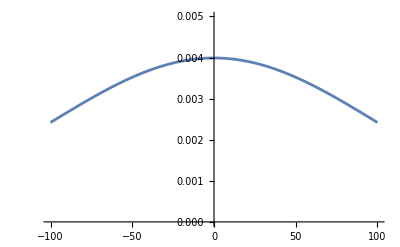

```mathematica
Plot[1/(√(2Pi) w)Exp[-Subscript[α, o]^2/(2 w^2)]/.w->100,{Subscript[α, o],-100, 100}, PlotRange->{{-100,100},{0,0.005}}]
```

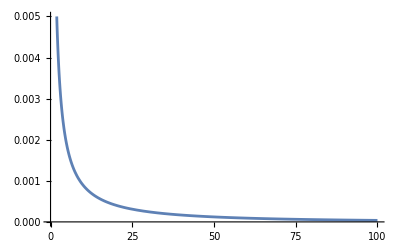

```mathematica
Plot[u^u/Gamma[u] t^(u-1)Exp[-u*t]/.u->0.01,{t,0, 100}, PlotRange->{{0,100},{0,0.005}}]
```

## The Posterior

Well the posterior is the high-dimensional function we are trying to sample using Monte Carlo methods. It is the product of the three likelihood equations and the five prior equations above:

P(t,α_0,t_α,β_(0,)t_β,{α_i},{β_i})=1/(√(2π/t))^(i·j)e^(-t∑_(i,j) (y_(i,j)-α_i-β_i v_(i,j))^2/2)·1/(√(2π/t_α))^ie^(-t_α∑_i (α_i-α_0)^2/2)·1/(√(2π/t_β))^ie^(-t_β∑_i (β_i-β_0)^2/2)·
                1/(√(2π)w)e^(-α_0^2/2 w^2)·1/(√(2π)w)e^(-β_0^2/2 w^2)·u^u/(Γ(u))t^(u-1)e^-ut·u^u/(Γ(u))t_α^(u-1)e^(-u t_α)·u^u/(Γ(u))t_β^(u-1)e^(-u t_β)

                ÷ the most horrible denominator you have yet encountered by far

This is our function of 217 parameters. I can’t even look at this function in its present form and see what it means. Let’s rewrite it without all the constant factors:

P(t,α_0,t_α,β_(0,)t_β,{α_i},{β_i})∝t^(u-1+i·j/2)e^(-t∑_(i,j) (y_(i,j)-α_i-β_i v_(i,j))^2/2)·t_α^(u-1+i/2)e^(-t_α∑_i (α_i-α_0)^2/2)·t_β^(u-1+i/2)e^(-t_β∑_i (β_i-β_0)^2/2)e^(-α_0^2/2 w^2)e^(-β_0^2/2 w^2)e^-ut e^(-u t_α)e^(-u t_β)

Notice that in ignoring the constants, I couldn’t get rid of all the powers of the various t’s. Those are not constants.

Now it is up to us to see the way this thing factors. Rewrite:

e^(-t∑_(i,j) (y_(i,j)-α_i-β_i τ_(i,j))^2/2)=∏_i e^(-t∑_j (y_(i,j)-α_i-β_i τ_(i,j))^2/2)

And rewrite:

e^(-t_α∑_i (α_i-α_0)^2/2)=∏_i e^(-(t_α(α_i-α_0))^2/2)

And rewrite:

e^(-t_β∑_i (β_i-β_0)^2/2)=∏_i e^(-(t_β(β_i-β_0))^2/2)

Then

P(t,α_0,t_α,β_(0,)t_β,{α_i},{β_i})=t^(u-1+i·j/2)∏_i e^(-t∑_j (y_(i,j)-α_i-β_i v_(i,j))^2/2)·t_α^(u-1+i/2)∏_i e^(-(t_α(α_i-α_0))^2/2)·t_β^(u-1+i/2)∏_i e^(-(t_β(β_i-β_0))^2/2)e^(-α_0^2/2 w^2)e^(-β_0^2/2 w^2)e^-ut e^(-u t_α)e^(-u t_β)

### The Power of Factorization

We have the factorization we said we were going to get in the previous write-up:

* https://brianhill.github.io/bayesian-statistics/resources/MonteCarloMethodsWhyDoTheyWork-III.nb.pdf

The factorization means that whenever we move in an α_i or β_i direction, we can treat as a constant multiplier the factors involving 210 of the parameters. In other words, we need only consider the tangled factors involving 7 parameters, which are:

P(t,α_0,t_α,β_(0,)t_β,α_i,β_i)∝e^(-t∑_j (y_(i,j)-α_i-β_i v_(i,j))^2/2)·e^(-(t_α(α_i-α_0))^2/2)·e^(-(t_β(β_i-β_0))^2/2)

The products are gone, and the set symbols around α_i and β_i are gone. This might still be a somewhat complicated computation. However, thinking of the first five of these parameters as given, as we bounce around in α_i and β_i we just have exponentials of quadratic functions of α_i and β_i. In other words, we just have ordinary Gaussians. And we know how to sample ordinary Gaussians!

Let me be even more explicit. I’ll just call the proportionality constant A for awful. I’ll imagine bouncing from α_i to α_i'. Then the new probability over the old proability is:

(P(t,α_0,t_α,β_(0,)t_β,α_i',β_i))/(P(t,α_0,t_α,β_(0,)t_β,α_i,β_i))=Ae^(-t∑_j (y_(i,j)-α_i'-β_i v_(i,j))^2/2)·e^(-(t_α(α_i-α_0))^2/2)·e^(-(t_β(β_i-β_0))^2/2)

### The Recalcitrant Axes

Let’s look at one of the recalcitrant axes, like the first one, s. Imagining that all the other four of the recalcitrant parameters and all of the 212 α_i and β_i are fixed, we can treat everything that has no dependence on s as a constant. We are left with:

P(s,α_0,s_α,β_(0,)s_β,{α_i},{β_i})∝s^(i·j/2+v-1)e^(-s∑_(i,j) (y_(i,j)-α_i-β_i τ_(i,j))^2/2)e^-vs

Is that not just a new Gamma distribution in s? Sure, the parameters that characterize this particular Gamma distribution involve 212 other parameters and the titer data. Regardless of the formula for the parameters, we know how to sample a Gamma distribution. Remember that those other 212 parameters are just fixed numbers when we are moving along the s axis.

Let’s do one more recalcitrant axis just to see that we didn’t get lucky with the first one. How about the α_0 axis? We can treat everything with no dependence on α_0 as a constant. We are left with:

P(s,α_0,s_α,β_(0,)s_β,α_i,β_i)∝e^(-s_α∑_i (α_i-α_0)^2/2)e^(-α_0^2/2 w^2)

That’s just a Gaussian in α_0! Sure it involves 106 other parameters, but it is still a Gaussian and we know how to sample it. Remember that those other 106 parameters are fixed when we are moving along the α_0 axis.

## The Conclusion

You still have to write a lot of code to sample the posterior distribution with Gibbs sampling. Maybe that is why it took until 1994 for the BUGS program to mature and be published.

However, moving one axis at a time has for every parameter become a low-dimensional and tractable problem involving distributions we are already thoroughly familiar with.

That means we can get a representative distribution out of this 217-dimensional space using Gibbs sampling. Using these representative samples, we can inquire about the most important results from the Hepatitis B study. The parameter we are most interested in would be α_0. Remember that roughly-speaking, α_0 controls the mean of the α_i via the likelihood function,

P_α=1/(√(2π)σ_α)^i e^(-∑_i (α_i-α_0)^2/2 σ_α^2)

and the α_i represent the rate of increase of the Hepatitis B titers. We would also be interested in the variance of the α_i and that roughly speaking is in s_α=σ_α^2. However, we don’t want to know the typical values of these things in the prior. We want to know what they central values and their ranges are in the posterior.

The goal of looking closely at this case study is to see how the posterior can be practically sampled using Gibbs sampling, such as with the BUGS program. The reference for the BUGS program is Gilks, Thomas, and Spiegelhalter, “A language and program for complex Bayesian modelling,” The Statistician, 43 (1994) 169-177, but I haven’t ever used the program or studied the original reference. I learned this stuff from Donovan and Mickey and Chapters 1 and 2 of Spiegelhalter, Best, Gilks, and Inskip.